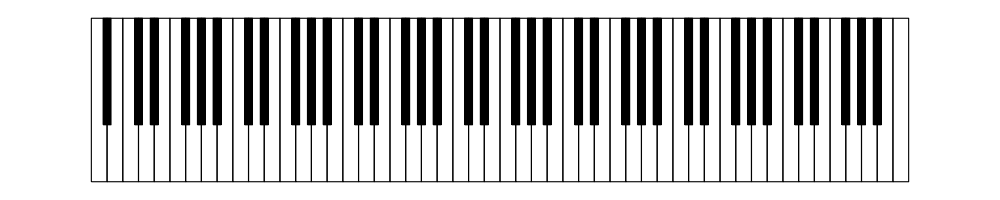

```mathematica
dw[k_]:=If[MemberQ[{0,3},Mod[k,7]],1,2];
w[n_]:=Which[n≤-1,-Sum[dw[k],{k,n+1,0}],n≥1,Sum[dw[k],{k,1,n}],True,0];

dh[k_]:=If[MemberQ[{0,2},Mod[k,5]],3,2];
h[n_]:=1+Which[n≤-1,-Sum[dh[k],{k,n+1,0}],n≥1,Sum[dh[k],{k,1,n}],True,0];

d[k_]:=If[MemberQ[{0,2},Mod[k,5]],2,1];
a[n_]:=0.5+Which[n≤-1,-Sum[d[k],{k,n+1,0}],n≥1,Sum[d[k],{k,1,n}],True,0];

Graphics[{

Table[With[{i=i},
Button[
{White,EdgeForm[Black],Rectangle[{i,0},{i+1,6.6}]},
EmitSound[Sound[SoundNote[w[i],1,"BrightPiano"]]]
]
],{i,-23,28}],

Table[With[{j=j},
Button[
{Black,EdgeForm[Black],Rectangle[{a[j]+ 0.25,2.3},{a[j]+0.75,6.6}]},
EmitSound[Sound[SoundNote[h[j],1,"BrightPiano"]]]
]
],{j,-16,19}]},

ImageSize->1000]
```